```mathematica
SeedRandom[4951035];
```

```mathematica
RandomInteger[];
```

```mathematica
Histogram[RandomVariate[NormalDistribution[3,1],100000]];
```

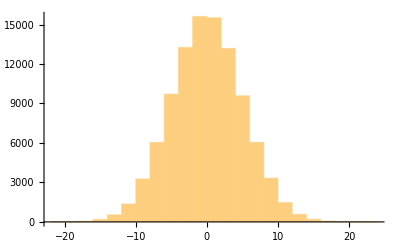
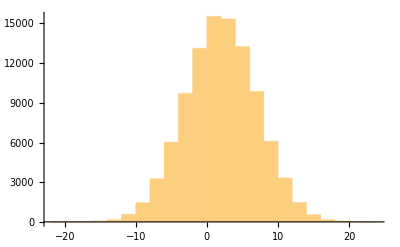
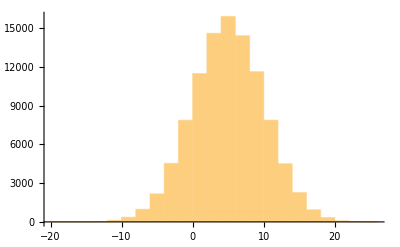

```mathematica
Table[Histogram[RandomVariate[NormalDistribution[i,5],100000]],{i,{0,2,5}}]
```

```mathematica
PDF[NormalDistribution[3,5],x]
```

(ⅇ^(-1/50 (-3+x)^2))/(5 √(2 π))

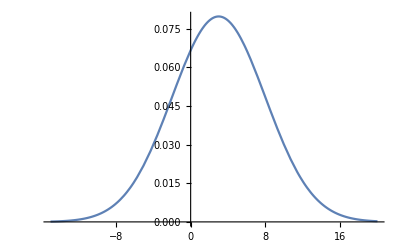

```mathematica
Plot[PDF[NormalDistribution[3,5],x],{x,-15,20}]
```

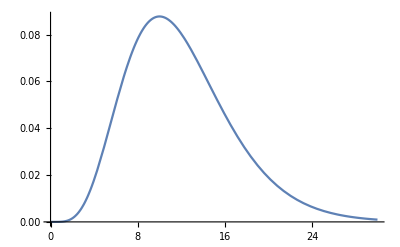

```mathematica
Plot[PDF[ChiSquareDistribution[12],x],{x,0,30}]
(*12 degrees of freedom*)
```

```mathematica
(*central limit theorem
think about flipping a coin and counting heads (0 or 1)*)
```

```mathematica
SeedRandom[1234]
sumsofcoinflips =Table[Total[RandomInteger[{0,1},30]],{i,10000}];
```

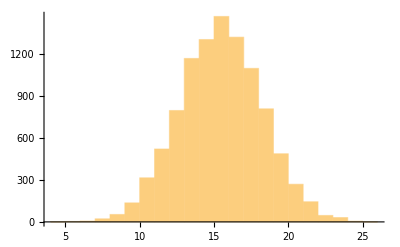

```mathematica
Histogram[sumsofcoinflips]
```